{{m3→c/(6 ε),m2→c/2,m1→(c ε)/2,m0→(c ε^2)/6,r1→0,r0→(c ε^2)/3}}

y_L(x;c,ε) = 0

y_L'(x;c,ε) = 0

y_L''(x;c,ε) = 0

y_M(x;c,ε) = c\ x^2/2 + c\ x^3/6\ ε + c\ x\ ε/2 + c\ ε^2/6

y_M'(x;c,ε) = c\ x + c\ x^2/2\ ε + c\ ε/2

y_M''(x;c,ε) = c + c\ x/ε

y_R(x;c,ε) = c\ x^2 + c\ ε^2/3

y_R'(x;c,ε) = 2\ c\ x

y_R''(x;c,ε) = 2\ c

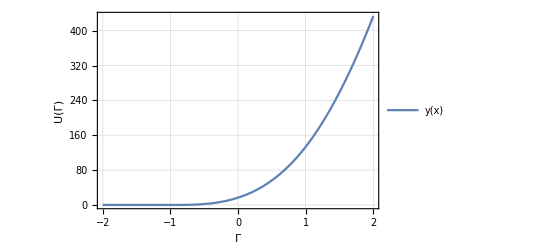

```mathematica
ClearAll["`*"];

yL[x_]:=0;
yR[x_]:=c x^2+r1 x+r0;
yM[x_]:=m3 x^3+m2 x^2+m1 x+m0;

bcL1=yM[-ε]==yL[-ε];
bcL2=yM'[-ε]==yL'[-ε];
bcL3=yM''[-ε]==yL''[-ε];
bcR1=yM[ε]==yR[ε];
bcR2=yM'[ε]==yR'[ε];
bcR3=yM''[ε]==yR''[ε];

sols=Solve[{bcL1,bcL2,bcL3,bcR1,bcR2,bcR3},{m3,m2,m1,m0, r1,r0}]

Set@@@sols[[1]];

StringForm["y_L(x;c,ε) = ``" ,yL[x]]
StringForm["y_L'(x;c,ε) = ``" ,yL'[x]]
StringForm["y_L''(x;c,ε) = ``" ,yL''[x]]

StringForm["y_M(x;c,ε) = ``" ,yM[x]]
StringForm["y_M'(x;c,ε) = ``" ,yM'[x]]
StringForm["y_M''(x;c,ε) = ``" ,yM''[x]]

StringForm["y_R(x;c,ε) = ``" ,yR[x]]
StringForm["y_R'(x;c,ε) = ``" ,yR'[x]]
StringForm["y_R''(x;c,ε) = ``" ,yR''[x]]

yLinterval[x_]:={yL[x],x≤-ε};
yMinterval[x_]:={yM[x],-ε≤x≤ε};
yRinterval[x_]:={yR[x],ε≤x};
y[x_]:=Piecewise[{yLinterval[x],yMinterval[x],yRinterval[x]}]
c=100;ε=1;
yplot=Plot[y[x],{x,-2ε,2ε},Exclusions->None,FrameLabel->{"Γ","U(Γ)"},PlotTheme->"Detailed"];
Show[yplot]
```

```mathematica
3^(1/3)
```

3^(1/3)

```mathematica
N[3^(1/3)]
```

1.44225

```mathematica
NumberForm[1.4422495703074083,15]
```

1.44224957030741